```mathematica
(*This notebook computes scattering of a monochromatic pulse, or of a spatially gaussian pulse off a Schwarzschild black hole*)
```

## Monochromatic pulse in Schwarzschild

```mathematica
M=1;
f=1-2M/r;f1=D[f,r];

(*define tortoise coordinate*)rt=Integrate[1/f,r];

l=0;
r1=2*(1+10^(-4));

ii=0;

Nmaxx=600;
While[ii<Nmaxx+1,
w=0.002+2*10^(-3)*ii;

(*Numerical infinity is chosen such that the domain always contains a large number of wavelengths, thus ensuring we are in the wave zone*)r2=100/w;

ahor=(ⅈ (1+l+l^2))/(2 M (ⅈ+4 M w));bhor=-(2 l^3+l^4+12 ⅈ M w+l (2+8 ⅈ M w)+l^2 (3+8 ⅈ M w))/(16 M^2 (-1+6 ⅈ M w+8 M^2 w^2));

(*Expanded field equation close to the horizon to get more accurate behavior*)
Hor=(1+ahor*(r-2*M)+bhor*(r-2*M)^2)*Exp[-I*w*rt];

BC=Hor/.r->r1;
BC1=D[Hor,r]/.r->r1;
EQ=f^2*D[y[r],{r,2}]+f*f1*D[y[r],{r,1}]+(w^2-f*(l*(l+1)/r^2+f1/r))*y[r];

sol=NDSolve[{EQ==0,y[r1]==BC,y'[r1]==BC1},y,{r,r1,r2}(*,
            AccuracyGoal -> 18, PrecisionGoal -> 18,
                             WorkingPrecision -> 24*),MaxSteps->340000];

ain=-(ⅈ l (1+l))/(2 w);bin=(2 l+l^2-2 l^3-l^4-4 ⅈ (M) w)/(8 w^2);cin=(ⅈ l (12+4 l-15 l^2-5 l^3+3 l^4+l^5)-12 (-2+3 l+3 l^2) (M) w)/(48 w^3);din=1/(384 w^4)(-56 l^5-14 l^6+4 l^7+l^8+4 l^3 (49+72 ⅈ M w)+l^4 (49+144 ⅈ M w)-144 (M) w (-2 ⅈ+3 M w)-48 ⅈ l (-3 ⅈ+14 M w)-12 ⅈ l^2 (-3 ⅈ+44 M w));
aout=(ⅈ l (1+l))/(2 w);bout=(2 l+l^2-2 l^3-l^4+4 ⅈ (M) w)/(8 w^2);cout=(15 ⅈ l^3+5 ⅈ l^4-3 ⅈ l^5-ⅈ l^6+24 (M) w-12 l (ⅈ+3 M w)-4 l^2 (ⅈ+9 M w))/(48 w^3);dout=1/(384 w^4)(-56 l^5-14 l^6+4 l^7+l^8+4 l^3 (49-72 ⅈ M w)+l^4 (49-144 ⅈ M w)-144 (M) w (2 ⅈ+3 M w)+48 ⅈ l (3 ⅈ+14 M w)+12 ⅈ l^2 (3 ⅈ+44 M w));

yinf=y[r2]/.sol[[1]];yinf1=y'[r2]/.sol[[1]];


rtinf=r+2 (M) Log[-2 M+r];

yinfana=Cin*(1+ain/r+bin/r^2+cin/r^3+din/r^4)*Exp[-I*w*rtinf]+Cout*(1+aout/r+bout/r^2+cout/r^3+dout/r^4)*Exp[I*w*rtinf]/.r->r2;
yinfana1=D[Cin*(1+ain/r+bin/r^2)*Exp[-I*w*rtinf]+Cout*(1+aout/r+bout/r^2)*Exp[I*w*rtinf],r]/.r->r2;
solcin=Solve[{yinf==yinfana,yinf1==yinfana1},{Cin,Cout}][[1]];

answer[ii]={w,(1-Abs[Cout]^2/Abs[Cin]^2)/.solcin};ii++]
```

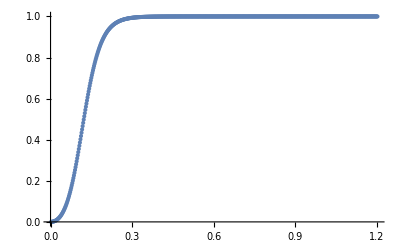

```mathematica
Tabe=Table[answer[ii],{ii,0,Nmaxx}];

(*Amplification Factor*)Amp=Table[{N[Tabe[[i,1]]],Tabe[[i,2]]},{i,1,Length[Tabe]}];
ListPlot[Amp,PlotRange->All]
```

## Numerics in frequency - domain for Schwarzschild: scattering of a Gaussian

```mathematica
M=1;
f=1-2M/r;f1=D[f,r];

(*define tortoise coordinate*)rt=Integrate[1/f,r];

l=1;

(*Initial data I, which I consider to be only psidot*)Initdata=Exp[-(r+2 Log[-2+r]-r0)^2/sigma^2];

(*r0 is the location, in tortoise coordinates, of the peak of the Gaussian initial data*)r0=10;

(*sigma is the width of the Gaussian wavepacket*)sigma=6;

r1=2*(1+10^(-4));
(*[r1,r2] define the integration interval over the source and avoids integrating over too large and unnecessary a domain:*)
rsource1=r1;
rsource2=r0+4*sigma;

ii=0;

Nmaxx=600;
While[ii<Nmaxx+1,
w=0.002+2*10^(-3)*ii;

(*Numerical infinity is chosen such that the domain always contains a large number of wavelengths, thus ensuring we are in the wave zone*)r2=100/w;

ahor=(ⅈ (1+l+l^2))/(2 M (ⅈ+4 M w));bhor=-(2 l^3+l^4+12 ⅈ M w+l (2+8 ⅈ M w)+l^2 (3+8 ⅈ M w))/(16 M^2 (-1+6 ⅈ M w+8 M^2 w^2));

(*Expanded field equation close to the horizon to get more accurate behavior*)Hor=(1+ahor*(r-2*M)+bhor*(r-2*M)^2)*Exp[-I*w*rt];

BC=Hor/.r->r1;
BC1=D[Hor,r]/.r->r1;
EQ=f^2*D[y[r],{r,2}]+f*f1*D[y[r],{r,1}]+(w^2-f*(l*(l+1)/r^2+f1/r))*y[r];

sol=NDSolve[{EQ==0,y[r1]==BC,y'[r1]==BC1},y,{r,r1,r2}(*,
            AccuracyGoal -> 18, PrecisionGoal -> 18,
                             WorkingPrecision -> 24*),MaxSteps->340000];

ain=-(ⅈ l (1+l))/(2 w);bin=(2 l+l^2-2 l^3-l^4-4 ⅈ (M) w)/(8 w^2);cin=(ⅈ l (12+4 l-15 l^2-5 l^3+3 l^4+l^5)-12 (-2+3 l+3 l^2) (M) w)/(48 w^3);din=1/(384 w^4)(-56 l^5-14 l^6+4 l^7+l^8+4 l^3 (49+72 ⅈ M w)+l^4 (49+144 ⅈ M w)-144 (M) w (-2 ⅈ+3 M w)-48 ⅈ l (-3 ⅈ+14 M w)-12 ⅈ l^2 (-3 ⅈ+44 M w));
aout=(ⅈ l (1+l))/(2 w);bout=(2 l+l^2-2 l^3-l^4+4 ⅈ (M) w)/(8 w^2);cout=(15 ⅈ l^3+5 ⅈ l^4-3 ⅈ l^5-ⅈ l^6+24 (M) w-12 l (ⅈ+3 M w)-4 l^2 (ⅈ+9 M w))/(48 w^3);dout=1/(384 w^4)(-56 l^5-14 l^6+4 l^7+l^8+4 l^3 (49-72 ⅈ M w)+l^4 (49-144 ⅈ M w)-144 (M) w (2 ⅈ+3 M w)+48 ⅈ l (3 ⅈ+14 M w)+12 ⅈ l^2 (3 ⅈ+44 M w));

yinf=y[r2]/.sol[[1]];yinf1=y'[r2]/.sol[[1]];


rtinf=r+2 (M) Log[-2 M+r];

yinfana=Cin*(1+ain/r+bin/r^2+cin/r^3+din/r^4)*Exp[-I*w*rtinf]+Cout*(1+aout/r+bout/r^2+cout/r^3+dout/r^4)*Exp[I*w*rtinf]/.r->r2;
yinfana1=D[Cin*(1+ain/r+bin/r^2)*Exp[-I*w*rtinf]+Cout*(1+aout/r+bout/r^2)*Exp[I*w*rtinf],r]/.r->r2;
solcin=Solve[{yinf==yinfana,yinf1==yinfana1},{Cin,Cout}][[1]];

Aint=NIntegrate[Initdata*y[r]/.sol//Release,{r,rsource1,rsource2}(*,WorkingPrecision->8,PrecisionGoal->8,MaxRecursion->6*)][[1]];

answer[ii]={w,Cin/.solcin[[1]],Psi=Aint/(2*I*w*Cin)/.solcin[[1]],P=w^2*Abs[Psi]^2};ii++]
```

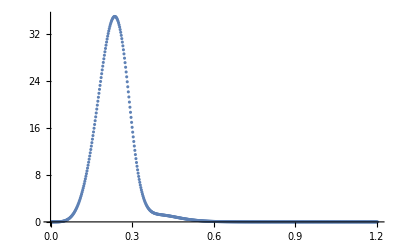

```mathematica
Tabe=Table[answer[ii],{ii,0,Nmaxx}];

(*Complex, fourier-domain waveform*)Wave=Table[{N[Tabe[[i,1]]],Tabe[[i,3]],Tabe[[i,4]]},{i,1,Length[Tabe]}];

(*Flux*)Tabepower1=Table[{Tabe[[i,1]],Tabe[[i,4]]},{i,1,Length[Tabe]}];ListPlot[Tabepower1,PlotRange->All]
```

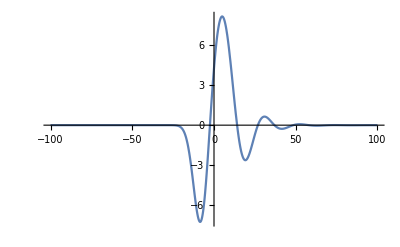

```mathematica
(*Bromwich integral to compute inverse*)Wavetime2[t_]:=1/2*Pi*Sum[Re[Wave[[i,2]]*Exp[-I*Wave[[i,1]]*(t)]]*(Wave[[i+1,1]]-Wave[[i,1]]),{i,1,Length[Wave]-1}];

Plot[Wavetime2[t],{t,-100,100},PlotRange->All]
```

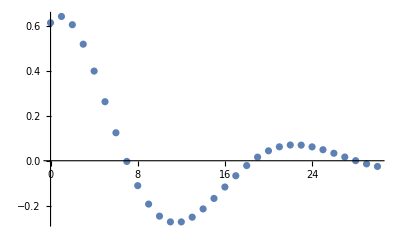

```mathematica
(*selection of the ringdown phase to estimate the QNM frequency*)ringdownpart=Table[{t-30,Wavetime2[t]},{t,30,60}];

ListPlot[ringdownpart]
```

```mathematica
par=FindFit[ringdownpart,a0*Exp[-wi*t]*Cos[wr*t+a1]+a2,{a0,a1,a2,wr,wi},t]
```

{a0→0.743254,a1→0.521267,a2→-0.021036,wr→-0.290629,wi→0.0896584}

```mathematica
Leaver method yields (see BCW, https://arxiv.org/abs/0905.2975):w= 0.2929361329967782-0.09765998891161318 ⅈ
```

## Kerr scalars

```mathematica
M=1;
ar=0.9;
rplus=M+Sqrt[M^2-ar^2];
rminus=M-Sqrt[M^2-ar^2];
Omega=ar/(2*M*rplus);
Delta=r^2+ar^2-2*M*r;Delta1=D[Delta,r];kabs=Abs[m];

l=1;
m=1;

r1=rplus*(1+10^(-6));
r2=500/w;
```

```mathematica
i=0;

While[i<100,
w=0.01+0.01*i;
NITMAX=100;γang=Function[n,2*w*ar*(n+kabs)];
βang=Function[n,n*(n-1)+2*n*(kabs+1-2*ar*w)-(2*ar*w*(kabs+1)-kabs*(kabs+1))-ar^2*w^2-Akjm];
αang=Function[n,-2*(n+1)*(n+Abs[m]+1)];Leaver31Ang[Sep_]:=Module[{Rn},
For[{n=NITMAX;Rn=-1.0;},n>0,{Rn=γang[n]/(βang[n]-αang[n]*Rn);n--;}];Rn];Leaver33Ang[Sep_]:=βang[0]/αang[0]-Leaver31Ang[Sep];FR=FindRoot[Leaver33Ang[Sep]==0,{Akjm,l*(l+1)}];

Alm=FR[[1]][[2]];
sigma=(rplus^2+ar^2)*(w-m*Omega)/(rplus-rminus);

BC=(r-rplus)^(-I*sigma)/.r->r1;
BC1=D[(r-rplus)^(-I*sigma),r]/.r->r1;

sol=NDSolve[{Delta*D[y[r],{r,2}]+Delta1*D[y[r],{r,1}]+((w*(r^2+ar^2)-m*ar)^2/Delta-Alm+2*m*ar*w-w^2*ar^2)*y[r]==0,y[r1]==BC,y'[r1]==BC1},y,{r,r1,r2},
            (*AccuracyGoal -> 14, PrecisionGoal -> 14,
                             WorkingPrecision -> 20,*)MaxSteps->1000000];
yr2=y[r2]/.sol[[1]];y1r2=y'[r2]/.sol[[1]];
rt=(r (rminus-rplus)+(ar^2+rminus^2) Log[r-rminus]-(ar^2+rplus^2) Log[r-rplus])/(rminus-rplus);
aout=(ⅈ (Alm+ar^2 w^2))/(2 w);
bout=-((-2+Alm) Alm-4 ⅈ M w+2 ar (ar+Alm ar-4 ⅈ m M) w^2+ar^4 w^4)/(8 w^2);
ain=-(ⅈ (Alm+ar^2 w^2))/(2 w);
bin=-((-2+Alm) Alm+4 ⅈ M w+2 ar (ar+Alm ar+4 ⅈ m M) w^2+ar^4 w^4)/(8 w^2);
fim=Solve[{yr2==Aout(1+aout/r+bout/r^2)*Exp[I*w*rt]*r^(-1)+Ain(1+ain/r+bin/r^2)*Exp[-I*w*rt]*r^(-1)/.r->r2,y1r2==D[Aout(1+aout/r+bout/r^2)*Exp[I*w*rt]*r^(-1)+Ain(1+ain/r+bin/r^2)*Exp[-I*w*rt]*r^(-1),r]/.r->r2},{Ain,Aout}];Ain0=fim[[1]][[1]][[2]];Aout0=fim[[1]][[2]][[2]];
Absor[i]={w,(1-Abs[Aout0]^2/Abs[Ain0]^2)};
i=i+1];
```

```mathematica
(*This gives 1-RR^2, which is negative since we are in the superradiant regime*)Absor2=Table[{Absor[i][[1]],Absor[i][[2]]},{i,0,50}]
```

{{0.01,-3.78515×10^-7},{0.02,-2.87051×10^-6},{0.03,-9.20975×10^-6},{0.04,-0.0000207965},{0.05,-0.0000387579},{0.06,-0.0000639952},{0.07,-0.0000972187},{0.08,-0.000138972},{0.09,-0.00018967},{0.1,-0.000249585},{0.11,-0.000318898},{0.12,-0.000397684},{0.13,-0.000485925},{0.14,-0.000583502},{0.15,-0.000690218},{0.16,-0.000805746},{0.17,-0.000929664},{0.18,-0.00106133},{0.19,-0.0011999},{0.2,-0.00134413},{0.21,-0.00149213},{0.22,-0.00164135},{0.23,-0.00178757},{0.24,-0.00192442},{0.25,-0.00204192},{0.26,-0.00212442},{0.27,-0.00214721},{0.28,-0.00207126},{0.29,-0.00183497},{0.3,-0.00134139},{0.31,-0.000438396},{0.32,0.00111145},{0.33,0.00367646},{0.34,0.00782238},{0.35,0.0144064},{0.36,0.0247007},{0.37,0.0405348},{0.38,0.0644123},{0.39,0.0994965},{0.4,0.149267},{0.41,0.216609},{0.42,0.302269},{0.43,0.40321},{0.44,0.512117},{0.45,0.619102},{0.46,0.715044},{0.47,0.794378},{0.48,0.855747},{0.49,0.900856},{0.5,0.93281},{0.51,0.954876}}

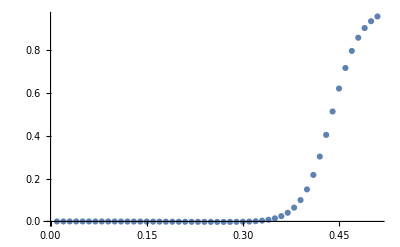

```mathematica
ListPlot[Absor2]
```

### Expansion at infinity

```mathematica
Integrate[(r^2+ar^2)/((r-rplus)*(r-rminus)),r]
```

(r (rminus-rplus)+(ar^2+rminus^2) Log[r-rminus]-(ar^2+rplus^2) Log[r-rplus])/(rminus-rplus)

```mathematica
y=Aout(1+aout/r+bout/r^2)*Exp[I*w*rt]*r^(-1)*0+Ain(1+ain/r+bin/r^2)*Exp[-I*w*rt]*r^(-1);
```

```mathematica
aout=(ⅈ (Alm+ar^2 w^2))/(2 w);
bout=-((-2+Alm) Alm-4 ⅈ M w+2 ar (ar+Alm ar-4 ⅈ m M) w^2+ar^4 w^4)/(8 w^2);
ain=-(ⅈ (Alm+ar^2 w^2))/(2 w);
bin->-((-2+Alm) Alm+4 ⅈ M w+2 ar (ar+Alm ar+4 ⅈ m M) w^2+ar^4 w^4)/(8 w^2);
```

```mathematica
rplus=M+Sqrt[M^2-ar^2];
rminus=M-Sqrt[M^2-ar^2];rt=(r (rminus-rplus)+(ar^2+rminus^2) Log[r-rminus]-(ar^2+rplus^2) Log[r-rplus])/(rminus-rplus);Delta=r^2+ar^2-2*M*r;Delta1=D[Delta,r];
WaveEq=Simplify[Exp[I*w*rt]*(Delta*D[y,{r,2}]+Delta1*D[y,{r,1}]+((w*(r^2+ar^2)-m*ar)^2/Delta-Alm+2*m*ar*w-w^2*ar^2)*y)];coef=Simplify[Normal[Series[WaveEq,{r,Infinity,2}]]]
```

```mathematica
(ⅈ Ain (Alm^2+2 Alm (-1+ar^2 w^2)+w (4 ⅈ M (1+2 ar m w)+w (2 ar^2+8 bin+ar^4 w^2))))/(2 r^2 w)
```

((0.+8.64109×10^-19 ⅈ) Ain)/r^2

```mathematica
FullSimplify[Solve[coef==0,bin]]
```

{{bin→-((-2+Alm) Alm+4 ⅈ M w+2 ar (ar+Alm ar+4 ⅈ m M) w^2+ar^4 w^4)/(8 w^2)}}

## References

```mathematica
[1]E. Barausse, V. Cardoso and P. Pani, "Can environmental effects spoil precision gravitational-wave astrophysics?", Phys.Rev.D89 (2014) no.10,104059
```

```mathematica
[2]R. Vicente, V. Cardoso and J. Lopes, "The Penrose process, superradiance and ergoregion instabilities", Phys.Rev.D89 (2014) no.10,104059; e-Print:arXiv:1803.08060[gr-qc]

[3]R. Brito, V. Cardoso and P. Pani, "Superradiance", Lect.Notes Phys.906 (2015) pp.1-237
```

```mathematica
[4]https://centra.tecnico.ulisboa.pt/network/grit/files/
```